```mathematica
Clear[Lx,Ly,l,mL,A,
sx2d,SX2D,
sy2d,SY2D,
cx2d,CX2D,
cy2d,CY2D,
cons,Cons]
```

```mathematica
Lx=20;
Ly=20;
l=10;
mL=10;
A=Lx*l+(Lx+1)*(Ly-l)
```

410

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,l-1}]
Do[Do[{sx2d[l Lx + j+k (Lx+1),l Lx + j+k (Lx+1)+1]=-I/2,sx2d[l Lx + j+k (Lx+1)+1,l Lx + j+k (Lx+1)]=I/2},{j,1,Lx}],{k,0,Ly-1-l}]
SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,l-1}]
Do[Do[{cx2d[l Lx + j+k (Lx+1),l Lx + j+k (Lx+1)+1]=1/2,cx2d[l Lx + j+k (Lx+1)+1,l Lx + j+k (Lx+1)]=1/2},{j,1,Lx}],{k,0,Ly-1-l}]
CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[j+k Lx,j+(1+k) Lx]=-I/2,sy2d[j+(1+k) Lx,j+k Lx]=I/2},{j,1,Lx}],{k,0,l-2}]
Do[Do[{sy2d[l Lx + j+k (Lx+1),l Lx + j+(k+1) (Lx+1)]=-I/2,sy2d[l Lx + j+(k+1) (Lx+1),l Lx + j+k (Lx+1)]=I/2},{j,1,Lx+1}],{k,0,Ly-2-l}]
Do[{sy2d[ j+(l-1)Lx, j+l Lx]=-I/2,sy2d[ j+l Lx,j+(l-1)Lx]=I/2},{j,1,mL}]
Do[{sy2d[ j+mL+(l-1)Lx,j+mL+1+l Lx]=-I/2,sy2d[j+mL+1+l Lx, j+mL+(l-1)Lx]=I/2},{j,1,Lx-mL}]
SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[j+k Lx,j+(1+k) Lx]=1/2,cy2d[j+(1+k) Lx,j+k Lx]=1/2},{j,1,Lx}],{k,0,l-2}]
Do[Do[{cy2d[l Lx + j+k (Lx+1),l Lx + j+(k+1) (Lx+1)]=1/2,cy2d[l Lx + j+(k+1) (Lx+1),l Lx + j+k (Lx+1)]=1/2},{j,1,Lx+1}],{k,0,Ly-2-l}]
Do[{cy2d[ j+(l-1)Lx, j+l Lx]=1/2,cy2d[ j+l Lx,j+(l-1)Lx]=1/2},{j,1,mL}]
Do[{cy2d[ j+mL+(l-1)Lx,j+mL+1+l Lx]=1/2,cy2d[j+mL+1+l Lx, j+mL+(l-1)Lx]=1/2},{j,1,Lx-mL}]
CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_]:=t*(KroneckerProduct[σ1,SX2D]+KroneckerProduct[σ2,SY2D])+KroneckerProduct[σ3,m*Cons+t0*(CX2D+CY2D)]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI[1.0,1.0,-1.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

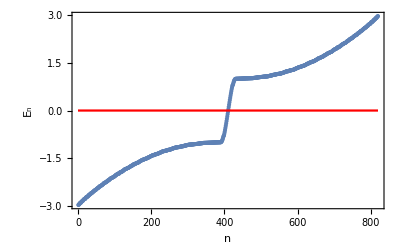

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
ValAHI
```

{{1,-2.9763},{2,-2.97409},{3,-2.95012},{4,-2.94899},{5,-2.91731},{6,-2.91455},{7,-2.91149},{8,-2.90698},{9,-2.87531},{10,-2.87215},{11,-2.86166},{12,-2.8575},{13,-2.84129},{14,-2.83675},{15,-2.81015},{16,-2.80185},{17,-2.79401},{18,-2.79119},{19,-2.78363},{20,-2.78195},{21,-2.7474},{22,-2.73972},{23,-2.73388},{24,-2.73183},{25,-2.7195},{26,-2.7078},{27,-2.70615},{28,-2.69994},{29,-2.66769},{30,-2.66515},{31,-2.65624},{32,-2.65346},{33,-2.63768},{34,-2.61802},{35,-2.61586},{36,-2.6126},{37,-2.60826},{38,-2.59989},{39,-2.58322},{40,-2.57116},{41,-2.56608},{42,-2.55973},{43,-2.54172},{44,-2.52985},{45,-2.52549},{46,-2.51217},{47,-2.51088},{48,-2.50842},{49,-2.49414},{50,-2.48421},{51,-2.46719},{52,-2.4656},{53,-2.45069},{54,-2.44412},{55,-2.43737},{56,-2.43532},{57,-2.42036},{58,-2.39586},{59,-2.39529},{60,-2.39274},{61,-2.38696},{62,-2.37466},{63,-2.36867},{64,-2.36131},{65,-2.35247},{66,-2.34822},{67,-2.33338},{68,-2.32777},{69,-2.32006},{70,-2.29949},{71,-2.29042},{72,-2.28087},{73,-2.27732},{74,-2.2723},{75,-2.26884},{76,-2.26358},{77,-2.25428},{78,-2.25077},{79,-2.23711},{80,-2.21856},{81,-2.21284},{82,-2.20657},{83,-2.20125},{84,-2.19657},{85,-2.19308},{86,-2.17218},{87,-2.16249},{88,-2.1545},{89,-2.14216},{90,-2.1348},{91,-2.13056},{92,-2.12851},{93,-2.12512},{94,-2.11328},{95,-2.10612},{96,-2.10142},{97,-2.09366},{98,-2.08475},{99,-2.08061},{100,-2.07641},{101,-2.06499},{102,-2.05771},{103,-2.03481},{104,-2.03064},{105,-2.02367},{106,-2.02057},{107,-2.00931},{108,-1.99773},{109,-1.99435},{110,-1.98997},{111,-1.98856},{112,-1.9871},{113,-1.98105},{114,-1.9574},{115,-1.9512},{116,-1.94608},{117,-1.94165},{118,-1.93715},{119,-1.92873},{120,-1.92443},{121,-1.91925},{122,-1.91221},{123,-1.89871},{124,-1.89557},{125,-1.88225},{126,-1.87027},{127,-1.86409},{128,-1.85278},{129,-1.84595},{130,-1.8458},{131,-1.84413},{132,-1.84087},{133,-1.83014},{134,-1.81836},{135,-1.81476},{136,-1.81176},{137,-1.81054},{138,-1.80562},{139,-1.79568},{140,-1.78878},{141,-1.77712},{142,-1.77311},{143,-1.7652},{144,-1.75915},{145,-1.75165},{146,-1.74157},{147,-1.7375},{148,-1.73353},{149,-1.73085},{150,-1.71547},{151,-1.70385},{152,-1.69623},{153,-1.69511},{154,-1.69491},{155,-1.6892},{156,-1.68364},{157,-1.67392},{158,-1.66777},{159,-1.66487},{160,-1.6573},{161,-1.65126},{162,-1.6483},{163,-1.64653},{164,-1.64254},{165,-1.63666},{166,-1.62832},{167,-1.62115},{168,-1.60777},{169,-1.60126},{170,-1.59786},{171,-1.59155},{172,-1.58869},{173,-1.57441},{174,-1.56645},{175,-1.56169},{176,-1.55745},{177,-1.55151},{178,-1.55067},{179,-1.54855},{180,-1.54434},{181,-1.53159},{182,-1.5312},{183,-1.52795},{184,-1.52209},{185,-1.51875},{186,-1.51812},{187,-1.50992},{188,-1.50883},{189,-1.49722},{190,-1.49253},{191,-1.48513},{192,-1.47891},{193,-1.47756},{194,-1.4772},{195,-1.46789},{196,-1.46461},{197,-1.45446},{198,-1.44227},{199,-1.43928},{200,-1.43347},{201,-1.4317},{202,-1.42212},{203,-1.4164},{204,-1.41031},{205,-1.40955},{206,-1.40774},{207,-1.4063},{208,-1.40457},{209,-1.3945},{210,-1.38717},{211,-1.38563},{212,-1.38041},{213,-1.3778},{214,-1.37679},{215,-1.37274},{216,-1.36678},{217,-1.3655},{218,-1.3613},{219,-1.35909},{220,-1.34847},{221,-1.34383},{222,-1.34104},{223,-1.33278},{224,-1.33205},{225,-1.32903},{226,-1.31799},{227,-1.31365},{228,-1.30985},{229,-1.29956},{230,-1.29727},{231,-1.29591},{232,-1.28572},{233,-1.28314},{234,-1.27918},{235,-1.27883},{236,-1.27759},{237,-1.27641},{238,-1.26936},{239,-1.26639},{240,-1.26505},{241,-1.26455},{242,-1.2601},{243,-1.25656},{244,-1.25514},{245,-1.24588},{246,-1.24198},{247,-1.24058},{248,-1.23822},{249,-1.23607},{250,-1.23374},{251,-1.2325},{252,-1.23174},{253,-1.22929},{254,-1.21865},{255,-1.21468},{256,-1.21025},{257,-1.204},{258,-1.2022},{259,-1.19831},{260,-1.19377},{261,-1.18622},{262,-1.18457},{263,-1.18274},{264,-1.17679},{265,-1.17532},{266,-1.16802},{267,-1.16569},{268,-1.16512},{269,-1.1646},{270,-1.16181},{271,-1.15934},{272,-1.15797},{273,-1.15614},{274,-1.15364},{275,-1.15247},{276,-1.15159},{277,-1.1495},{278,-1.14405},{279,-1.14103},{280,-1.1401},{281,-1.13729},{282,-1.13575},{283,-1.1313},{284,-1.12956},{285,-1.12782},{286,-1.12689},{287,-1.12465},{288,-1.1233},{289,-1.12028},{290,-1.11276},{291,-1.10728},{292,-1.10706},{293,-1.10481},{294,-1.10289},{295,-1.10187},{296,-1.09885},{297,-1.09607},{298,-1.09054},{299,-1.08661},{300,-1.08568},{301,-1.08394},{302,-1.07792},{303,-1.07724},{304,-1.0768},{305,-1.07664},{306,-1.0751},{307,-1.07335},{308,-1.07261},{309,-1.07192},{310,-1.07075},{311,-1.07038},{312,-1.06991},{313,-1.06759},{314,-1.06652},{315,-1.06505},{316,-1.06319},{317,-1.06223},{318,-1.06118},{319,-1.059},{320,-1.05766},{321,-1.05732},{322,-1.05592},{323,-1.05492},{324,-1.05226},{325,-1.05137},{326,-1.05102},{327,-1.04962},{328,-1.04651},{329,-1.04337},{330,-1.04278},{331,-1.04201},{332,-1.04025},{333,-1.03724},{334,-1.03684},{335,-1.03566},{336,-1.03232},{337,-1.03117},{338,-1.03069},{339,-1.03021},{340,-1.029},{341,-1.02589},{342,-1.02219},{343,-1.0214},{344,-1.0207},{345,-1.02063},{346,-1.01978},{347,-1.01968},{348,-1.01962},{349,-1.01953},{350,-1.01851},{351,-1.01796},{352,-1.01789},{353,-1.01781},{354,-1.01761},{355,-1.01636},{356,-1.01598},{357,-1.01538},{358,-1.01512},{359,-1.0145},{360,-1.01433},{361,-1.01422},{362,-1.01398},{363,-1.01261},{364,-1.01207},{365,-1.01159},{366,-1.01091},{367,-1.01067},{368,-1.01013},{369,-1.00969},{370,-1.00922},{371,-1.00904},{372,-1.00863},{373,-1.00739},{374,-1.00706},{375,-1.00586},{376,-1.00541},{377,-1.00514},{378,-1.0051},{379,-1.00478},{380,-1.0046},{381,-1.00357},{382,-1.00317},{383,-1.00234},{384,-1.00228},{385,-1.00227},{386,-1.0013},{387,-1.00121},{388,-1.00061},{389,-1.00058},{390,-1.0004},{391,-0.996067},{392,-0.985379},{393,-0.968905},{394,-0.945661},{395,-0.91563},{396,-0.87871},{397,-0.835076},{398,-0.800396},{399,-0.785281},{400,-0.730175},{401,-0.670716},{402,-0.607771},{403,-0.542024},{404,-0.473997},{405,-0.404095},{406,-0.332659},{407,-0.259993},{408,-0.18638},{409,-0.112096},{410,-0.0374098},{411,0.0374098},{412,0.112096},{413,0.18638},{414,0.259993},{415,0.332659},{416,0.404095},{417,0.473997},{418,0.542024},{419,0.607771},{420,0.670716},{421,0.730175},{422,0.785281},{423,0.800396},{424,0.835076},{425,0.87871},{426,0.91563},{427,0.945661},{428,0.968905},{429,0.985379},{430,0.996067},{431,1.0004},{432,1.00058},{433,1.00061},{434,1.00121},{435,1.0013},{436,1.00227},{437,1.00228},{438,1.00234},{439,1.00317},{440,1.00357},{441,1.0046},{442,1.00478},{443,1.0051},{444,1.00514},{445,1.00541},{446,1.00586},{447,1.00706},{448,1.00739},{449,1.00863},{450,1.00904},{451,1.00922},{452,1.00969},{453,1.01013},{454,1.01067},{455,1.01091},{456,1.01159},{457,1.01207},{458,1.01261},{459,1.01398},{460,1.01422},{461,1.01433},{462,1.0145},{463,1.01512},{464,1.01538},{465,1.01598},{466,1.01636},{467,1.01761},{468,1.01781},{469,1.01789},{470,1.01796},{471,1.01851},{472,1.01953},{473,1.01962},{474,1.01968},{475,1.01978},{476,1.02063},{477,1.0207},{478,1.0214},{479,1.02219},{480,1.02589},{481,1.029},{482,1.03021},{483,1.03069},{484,1.03117},{485,1.03232},{486,1.03566},{487,1.03684},{488,1.03724},{489,1.04025},{490,1.04201},{491,1.04278},{492,1.04337},{493,1.04651},{494,1.04962},{495,1.05102},{496,1.05137},{497,1.05226},{498,1.05492},{499,1.05592},{500,1.05732},{501,1.05766},{502,1.059},{503,1.06118},{504,1.06223},{505,1.06319},{506,1.06505},{507,1.06652},{508,1.06759},{509,1.06991},{510,1.07038},{511,1.07075},{512,1.07192},{513,1.07261},{514,1.07335},{515,1.0751},{516,1.07664},{517,1.0768},{518,1.07724},{519,1.07792},{520,1.08394},{521,1.08568},{522,1.08661},{523,1.09054},{524,1.09607},{525,1.09885},{526,1.10187},{527,1.10289},{528,1.10481},{529,1.10706},{530,1.10728},{531,1.11276},{532,1.12028},{533,1.1233},{534,1.12465},{535,1.12689},{536,1.12782},{537,1.12956},{538,1.1313},{539,1.13575},{540,1.13729},{541,1.1401},{542,1.14103},{543,1.14405},{544,1.1495},{545,1.15159},{546,1.15247},{547,1.15364},{548,1.15614},{549,1.15797},{550,1.15934},{551,1.16181},{552,1.1646},{553,1.16512},{554,1.16569},{555,1.16802},{556,1.17532},{557,1.17679},{558,1.18274},{559,1.18457},{560,1.18622},{561,1.19377},{562,1.19831},{563,1.2022},{564,1.204},{565,1.21025},{566,1.21468},{567,1.21865},{568,1.22929},{569,1.23174},{570,1.2325},{571,1.23374},{572,1.23607},{573,1.23822},{574,1.24058},{575,1.24198},{576,1.24588},{577,1.25514},{578,1.25656},{579,1.2601},{580,1.26455},{581,1.26505},{582,1.26639},{583,1.26936},{584,1.27641},{585,1.27759},{586,1.27883},{587,1.27918},{588,1.28314},{589,1.28572},{590,1.29591},{591,1.29727},{592,1.29956},{593,1.30985},{594,1.31365},{595,1.31799},{596,1.32903},{597,1.33205},{598,1.33278},{599,1.34104},{600,1.34383},{601,1.34847},{602,1.35909},{603,1.3613},{604,1.3655},{605,1.36678},{606,1.37274},{607,1.37679},{608,1.3778},{609,1.38041},{610,1.38563},{611,1.38717},{612,1.3945},{613,1.40457},{614,1.4063},{615,1.40774},{616,1.40955},{617,1.41031},{618,1.4164},{619,1.42212},{620,1.4317},{621,1.43347},{622,1.43928},{623,1.44227},{624,1.45446},{625,1.46461},{626,1.46789},{627,1.4772},{628,1.47756},{629,1.47891},{630,1.48513},{631,1.49253},{632,1.49722},{633,1.50883},{634,1.50992},{635,1.51812},{636,1.51875},{637,1.52209},{638,1.52795},{639,1.5312},{640,1.53159},{641,1.54434},{642,1.54855},{643,1.55067},{644,1.55151},{645,1.55745},{646,1.56169},{647,1.56645},{648,1.57441},{649,1.58869},{650,1.59155},{651,1.59786},{652,1.60126},{653,1.60777},{654,1.62115},{655,1.62832},{656,1.63666},{657,1.64254},{658,1.64653},{659,1.6483},{660,1.65126},{661,1.6573},{662,1.66487},{663,1.66777},{664,1.67392},{665,1.68364},{666,1.6892},{667,1.69491},{668,1.69511},{669,1.69623},{670,1.70385},{671,1.71547},{672,1.73085},{673,1.73353},{674,1.7375},{675,1.74157},{676,1.75165},{677,1.75915},{678,1.7652},{679,1.77311},{680,1.77712},{681,1.78878},{682,1.79568},{683,1.80562},{684,1.81054},{685,1.81176},{686,1.81476},{687,1.81836},{688,1.83014},{689,1.84087},{690,1.84413},{691,1.8458},{692,1.84595},{693,1.85278},{694,1.86409},{695,1.87027},{696,1.88225},{697,1.89557},{698,1.89871},{699,1.91221},{700,1.91925},{701,1.92443},{702,1.92873},{703,1.93715},{704,1.94165},{705,1.94608},{706,1.9512},{707,1.9574},{708,1.98105},{709,1.9871},{710,1.98856},{711,1.98997},{712,1.99435},{713,1.99773},{714,2.00931},{715,2.02057},{716,2.02367},{717,2.03064},{718,2.03481},{719,2.05771},{720,2.06499},{721,2.07641},{722,2.08061},{723,2.08475},{724,2.09366},{725,2.10142},{726,2.10612},{727,2.11328},{728,2.12512},{729,2.12851},{730,2.13056},{731,2.1348},{732,2.14216},{733,2.1545},{734,2.16249},{735,2.17218},{736,2.19308},{737,2.19657},{738,2.20125},{739,2.20657},{740,2.21284},{741,2.21856},{742,2.23711},{743,2.25077},{744,2.25428},{745,2.26358},{746,2.26884},{747,2.2723},{748,2.27732},{749,2.28087},{750,2.29042},{751,2.29949},{752,2.32006},{753,2.32777},{754,2.33338},{755,2.34822},{756,2.35247},{757,2.36131},{758,2.36867},{759,2.37466},{760,2.38696},{761,2.39274},{762,2.39529},{763,2.39586},{764,2.42036},{765,2.43532},{766,2.43737},{767,2.44412},{768,2.45069},{769,2.4656},{770,2.46719},{771,2.48421},{772,2.49414},{773,2.50842},{774,2.51088},{775,2.51217},{776,2.52549},{777,2.52985},{778,2.54172},{779,2.55973},{780,2.56608},{781,2.57116},{782,2.58322},{783,2.59989},{784,2.60826},{785,2.6126},{786,2.61586},{787,2.61802},{788,2.63768},{789,2.65346},{790,2.65624},{791,2.66515},{792,2.66769},{793,2.69994},{794,2.70615},{795,2.7078},{796,2.7195},{797,2.73183},{798,2.73388},{799,2.73972},{800,2.7474},{801,2.78195},{802,2.78363},{803,2.79119},{804,2.79401},{805,2.80185},{806,2.81015},{807,2.83675},{808,2.84129},{809,2.8575},{810,2.86166},{811,2.87215},{812,2.87531},{813,2.90698},{814,2.91149},{815,2.91455},{816,2.91731},{817,2.94899},{818,2.95012},{819,2.97409},{820,2.9763}}